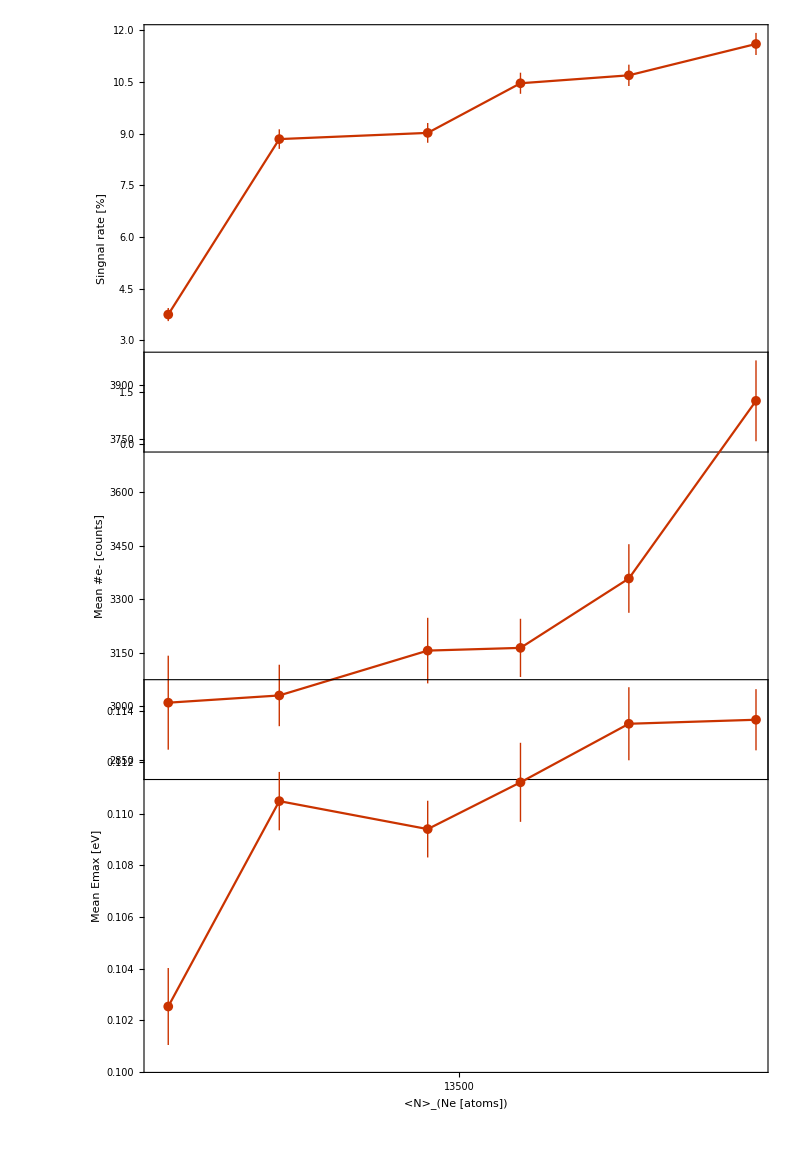

```mathematica
SIGNAL  Rate;
data=Table[{names[[n]],Length[list[[n]]]/100},{n,1,Length[list]}];
aux=data;
aux=aux/. {a_,b_}:> {a,Around[b,Sqrt[b*(100-b)/10000]]};

ticks=(*{#,ScientificForm[Nenum[#]],1}&/@names} *)Transpose[{names,names2}];(*data[[All,1]]*);

a=ListPlot[aux,PlotRange->Automatic,Joined->True,Frame->True,
PlotStyle->ColorData[112],LabelStyle->32,
FrameLabel->{{"Singnal rate [%]",None},{None,(*"Pulse cycles"*)"T_(Ne [K]) "}},
PlotMarkers->{Automatic, 10},ImageSize->600,
FrameTicks->{{Automatic,None},{None,ticks}},FrameTicksStyle->26];
Meanaelectrons;
list2={};
For[n=1,n≤Length[list],n++,
data=list[[n,All,1]];
ta=Mean[data];
stderr=standardError[data];
AppendTo[list2,{names[[n]],Around[ta,stderr]}];
]
list2=Sort[list2];
b=ListPlot[list2,PlotRange->Automatic,PlotStyle->ColorData[112],PlotMarkers->{Automatic, 10},Frame->True,FrameLabel->{,"Mean #e- [counts]"},LabelStyle->32,ImageSize->600,Joined->True,
FrameTicks->{{Automatic,None},{None,Automatic}},FrameTicksStyle->24];
MeanEnergy;
list2={};
For[n=1,n≤Length[list],n++,
data=list[[n,All,2]];
ta=Mean[data];
stderr=standardError[data];
AppendTo[list2,{names[[n]],Around[ta,stderr]}];
]
list2=Sort[list2];
c=ListPlot[list2,PlotRange->Automatic,PlotStyle->ColorData[112],PlotMarkers->{Automatic, 10},Frame->True,
FrameLabel->{"<N>_(Ne [atoms])","Mean Emax [eV]"},
LabelStyle->32,ImageSize->600,Joined->True,
FrameTicks->{{Automatic,None},{Range[1000,500000,2500],None}},FrameTicksStyle->22];




GraphicsColumn[{a,b,c},Spacings->-125,ImageSize->800]
```

```mathematica
Export["C:\\Users\\nano\\thesis\\Msc Thesis\\Images\\results\\MIR_Ne_DropletSize\\alltogether.png",%,"PNG"]
```

C:\Users\nano\thesis\Msc Thesis\Images\results\MIR_Ne_DropletSize\alltogether.png

```mathematica
Neon pulse duration-Graphics-
```

C:\Users\nano\thesis\Msc Thesis\Images\results\MIR_Ne_pulseduration\Alltogether.png

```mathematica
He pulse duration"C:\\Users\\nano\\thesis\\Msc Thesis\\Images\\results\\MIR_He_pulsescan\\raw\\Alltogether.png"
```

```mathematica
He CLuster size-Graphics-
```

```mathematica
He Argon-Graphics-
```

```mathematica
Neon droplet size-Graphics-
```

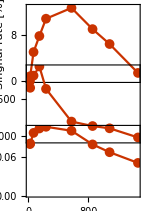
```mathematica
Neon Xe dop-Graphics-
```